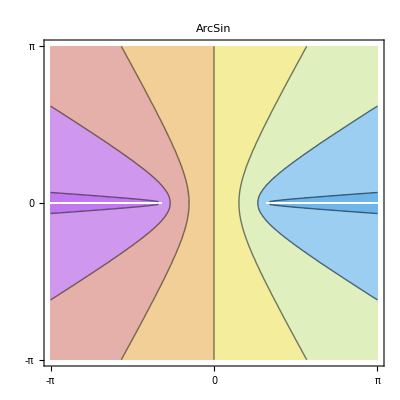
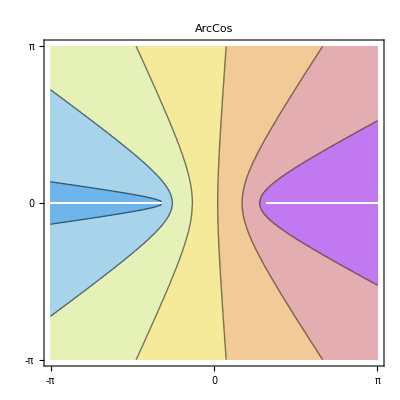
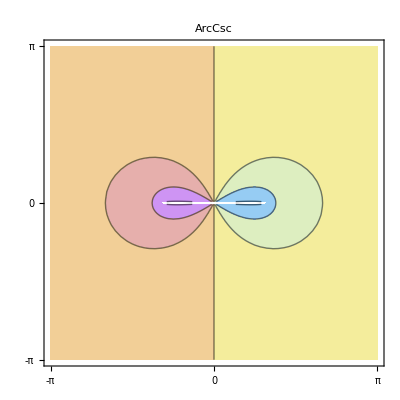
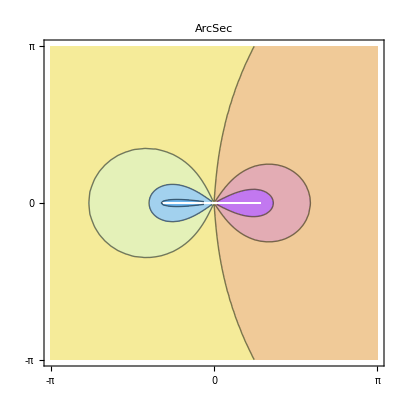
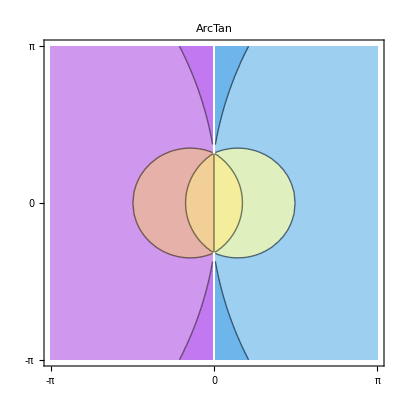
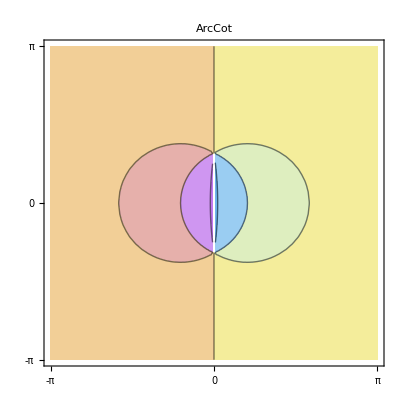

```mathematica
Table[
ContourPlot[
Re[f[x+I y]],{x,-Pi,Pi},{y,-Pi,Pi},PlotLabel->f,FrameTicks->{{-Pi,0,Pi},{-Pi,0,Pi}},ClippingStyle->Automatic,ColorFunction->"Pastel"
],
{f,{ArcSin,ArcCos,ArcCsc,ArcSec,ArcTan,ArcCot}}
]
```

{0.1,0.55,0.35}

{6.,1.2,0.3}

{0.0166667,0.458333,1.16667}

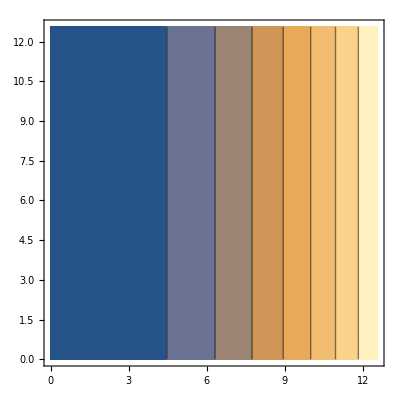

```mathematica
α={0.1,0.55,0.35}
β={6.0,1.2,0.3}
γ=α/β
N=; (*Atomi/m^3*)
Upl(x_):=
ContourPlot[x^2,{x,0,4 Pi},{y,0,4 Pi}]
```